# Mass String Bridge

-Graphics-

```mathematica
ClearAll["Global`*"]
$Assumptions={Subscript[y, _]>0&&Subscript[m, _]>0&&Subscript[F, _]>0&&Subscript[T, _]>0&&Subscript[L, 1]>0&&Subscript[L, 2]>0&&Subscript[L, 3]>0&&Subscript[L, 4]>0}
```

{y__>0&&m__>0&&F__>0&&T__>0&&L_1>0&&L_2>0&&L_3>0&&L_4>0}

## Setup

Establish variables for Sin[θ_n] = H_n

```mathematica
Subscript[H, 1]=Subscript[y, 1][t]/√(Subscript[L, 1]^2+(Subscript[y, 1][t])^2);
Subscript[H, 2]=(Subscript[y, 2][t]-Subscript[y, 1][t])/√(Subscript[L, 2]^2+(Subscript[y, 2][t]-Subscript[y, 1][t])^2);
Subscript[H, 3]=(Subscript[y, 3][t]-Subscript[y, 2][t])/√(Subscript[L, 3]^2+(Subscript[y, 3][t]-Subscript[y, 2][t])^2);
Subscript[H, 4]=-Subscript[y, 3][t]/√(Subscript[L, 4]^2+(Subscript[y, 3][t])^2);
```

## Equations of Motion

Assuming x axis is horizontal and positive towards the right. The y axis is vertical and positive points up. I define position vectors for all masses:

```mathematica
Subscript[r, 1]={Subscript[L, 1],Subscript[y, 1][t]};
Subscript[r, 2]={Subscript[r, 1][[1]]+Subscript[L, 2],Subscript[y, 2][t]};
Subscript[r, 3]={Subscript[r, 2][[1]]+Subscript[L, 3],Subscript[y, 3][t]};
Subscript[r, 4]={Subscript[r, 3][[1]]+Subscript[L, 4],0};
```

Define kinetic energy of a system:

```mathematica
KE=Sum[1/2 Subscript[m, k](D[Subscript[r, k][[1]],t]^2+D[Subscript[r, k][[2]],t]^2),{k,3}]//Simplify
```

1/2 (m_1 y_1'[t]^2+m_2 y_2'[t]^2+m_3 y_3'[t]^2)

Define potential energy of a system:

```mathematica
PE=-(Subscript[m, 1] g Subscript[r, 1][[2]]+Subscript[m, 2] g Subscript[r, 2][[2]]+Subscript[m, 3] g Subscript[r, 3][[2]])//Expand
```

-g m_1 y_1[t]-g m_2 y_2[t]-g m_3 y_3[t]

```mathematica
Lg=KE-PE//Expand
```

g m_1 y_1[t]+g m_2 y_2[t]+g m_3 y_3[t]+1/2 m_1 y_1'[t]^2+1/2 m_2 y_2'[t]^2+1/2 m_3 y_3'[t]^2

Define virtual work of a system:

```mathematica
Subscript[δW, 1] = (Subscript[F, 1][t]+T (-Subscript[H, 1]+Subscript[H, 2]))D[Subscript[r, 1][[2]],t]/.Subscript[y, n_]'[t]-> Subscript[δy, n]//Expand
Subscript[δW, 2] = (Subscript[F, 2][t]+T (-Subscript[H, 2]+Subscript[H, 3]))D[Subscript[r, 2][[2]],t]/.Subscript[y, n_]'[t]-> Subscript[δy, n]//Expand
Subscript[δW, 3] = (Subscript[F, 3][t]+T (-Subscript[H, 3]+Subscript[H, 4]))D[Subscript[r, 3][[2]],t]/.Subscript[y, n_]'[t]-> Subscript[δy, n]//Expand
```

δy_1 F_1[t]-(T δy_1 y_1[t])/(√(L_1^2+y_1[t]^2))-(T δy_1 y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))+(T δy_1 y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))

δy_2 F_2[t]+(T δy_2 y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T δy_2 y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T δy_2 y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))+(T δy_2 y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))

δy_3 F_3[t]-(T δy_3 y_3[t])/(√(L_4^2+y_3[t]^2))+(T δy_3 y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))-(T δy_3 y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))

Preallocate memory for the equations of motion:

```mathematica
eq={Null,Null,Null};
```

Assemble equations of motion:

```mathematica
Do[
Print[
eq[[k]]=D[D[Lg,Subscript[y, k]'[t]],t]+D[Lg,Subscript[y, k][t]]==Coefficient[Subscript[δW, k],Subscript[δy, k]]
],{k,3}
]//Simplify
```

g m_1+m_1 y_1''[t]==F_1[t]-(T y_1[t])/(√(L_1^2+y_1[t]^2))-(T y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))+(T y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))

g m_2+m_2 y_2''[t]==F_2[t]+(T y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))+(T y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))

g m_3+m_3 y_3''[t]==F_3[t]-(T y_3[t])/(√(L_4^2+y_3[t]^2))+(T y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))-(T y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))

## Equilibrium Points

Define the rules for equilibrium points and use them to simplify the equations of motion:

```mathematica
EqRules={Subscript[y, _]'[t]->0,Subscript[y, _]''[t]->0,Subscript[F, _][t]->0};
```

```mathematica
EqEqs=eq/.EqRules
```

{g m_1==-(T y_1[t])/(√(L_1^2+y_1[t]^2))-(T y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))+(T y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2)),g m_2==(T y_1[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T y_2[t])/(√(L_2^2+(-y_1[t]+y_2[t])^2))-(T y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))+(T y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2)),g m_3==-(T y_3[t])/(√(L_4^2+y_3[t]^2))+(T y_2[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))-(T y_3[t])/(√(L_3^2+(-y_2[t]+y_3[t])^2))}

Set refined rules for equilibrium points to solve for when there are small variations in y_n[t]. If you do not make this assumption, it will not be able to quickly solve for the equilibrium points.

```mathematica
EqRulesSmall = EqEqs/.(-Subscript[y, 1][t]+Subscript[y, 2][t])->0 /. (-Subscript[y, 2][t]+Subscript[y, 3][t])->0 /.(Subscript[y, 1][t])^2 -> 0 /.(Subscript[y, 3][t])^2->0
```

{g m_1==-(T y_1[t])/(√(L_1^2))-(T y_1[t])/(√(L_2^2))+(T y_2[t])/(√(L_2^2)),g m_2==(T y_1[t])/(√(L_2^2))-(T y_2[t])/(√(L_2^2))-(T y_2[t])/(√(L_3^2))+(T y_3[t])/(√(L_3^2)),g m_3==(T y_2[t])/(√(L_3^2))-(T y_3[t])/(√(L_3^2))-(T y_3[t])/(√(L_4^2))}

Solve the simplified equations of motion to determine the equilibrium points:

```mathematica
EqSols=Solve[EqRulesSmall,{Subscript[y, 1][t],Subscript[y, 2][t],Subscript[y, 3][t]}]/.{C[_]->0} //Simplify
```

{{y_1[t]→-(g L_1 (L_2 m_1+L_3 (m_1+m_2)+L_4 (m_1+m_2+m_3)))/(T (L_1+L_2+L_3+L_4)),y_2[t]→-(g (L_2 (L_3 m_2+L_4 (m_2+m_3))+L_1 (L_3 (m_1+m_2)+L_4 (m_1+m_2+m_3))))/(T (L_1+L_2+L_3+L_4)),y_3[t]→-(g L_4 (L_3 m_3+L_2 (m_2+m_3)+L_1 (m_1+m_2+m_3)))/(T (L_1+L_2+L_3+L_4))}}

## Linearized Equations of Motion About Equilibrium Points

Prepare for linearization about a general equilibrium point (this is a trick to do multivariate Taylor expansion):

```mathematica
subs={Subscript[y, p_][t]->Subscript[y, p][t]q,Subscript[y, p_]'[t]->Subscript[y, p]'[t]q,Subscript[y, p_]''[t]->Subscript[y, p]''[t]q};
```

```mathematica
taylorEqs=eq/.subs;
```

Using the trick from above, this returns the Linearize equations about some equilibrium point (ye_1, ye_2, ye_3) are:

```mathematica
linearizedEqs=Normal[
Series[taylorEqs,{q,0,1}]
]/.{q->1}
```

{g m_1+m_1 y_1''[t]==F_1[t]-(T y_1[t])/L_1-(T y_1[t])/L_2+(T y_2[t])/L_2,g m_2+m_2 y_2''[t]==F_2[t]+(T y_1[t])/L_2-(T y_2[t])/L_2-(T y_2[t])/L_3+(T y_3[t])/L_3,g m_3+m_3 y_3''[t]==F_3[t]+(T y_2[t])/L_3-(T y_3[t])/L_3-(T y_3[t])/L_4}

## Derive Eigenvalues

Assign the parameters that are given in the problem: m_i=m and L_i=L

Set new variable names for the equations of motion composed from the newly assigned parameters:

```mathematica
EqualMassEq=linearizedEqs/.Subscript[m, 1]-> m/.Subscript[m, 2]-> m/.Subscript[m, 3]-> m/.Subscript[L, 1]-> L/.Subscript[L, 2]-> L/.Subscript[L, 3]-> L/.Subscript[L, 4]-> L
```

{g m+m y_1''[t]==F_1[t]-(2 T y_1[t])/L+(T y_2[t])/L,g m+m y_2''[t]==F_2[t]+(T y_1[t])/L-(2 T y_2[t])/L+(T y_3[t])/L,g m+m y_3''[t]==F_3[t]+(T y_2[t])/L-(2 T y_3[t])/L}

The equations of motion for small oscillations about the stable equilibrium are:

```mathematica
Mm=Normal[CoefficientArrays[EqualMassEq,Table[Subscript[y, k]''[t],{k,3}]]][[2]]/(m); Mm//MatrixForm
Km=Normal[CoefficientArrays[EqualMassEq,Table[Subscript[y, k][t],{k,3}]]][[2]]/(T/L); Km//MatrixForm
Fm=EqualMassEq[[All,2]];Fm//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2)

(F_1[t]-(2 T y_1[t])/L+(T y_2[t])/L
F_2[t]+(T y_1[t])/L-(2 T y_2[t])/L+(T y_3[t])/L
F_3[t]+(T y_2[t])/L-(2 T y_3[t])/L)

Below are the eigenvectors of the system:

```mathematica
EqualMassES=Eigensystem[{Km,Mm}//N]
```

{{3.41421,2.,0.585786},{{-0.5,0.707107,-0.5},{-0.707107,4.8851×10^-17,0.707107},{0.5,0.707107,0.5}}}

## Modal Analysis

Normal modes:

```mathematica
EqualMassNM=EqualMassES[[2]]
```

{{-0.5,0.707107,-0.5},{-0.707107,4.8851×10^-17,0.707107},{0.5,0.707107,0.5}}

Natural frequencies:

```mathematica
EqualMassω=√(EqualMassES[[1]] T/(L m))//MatrixForm
```

(1.84776 √(T/(L m))
1.41421 √(T/(L m))
0.765367 √(T/(L m)))

Plot modes:

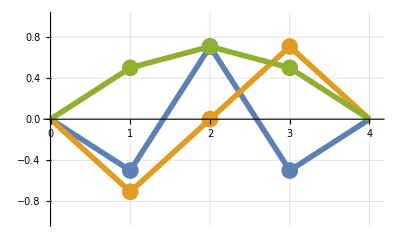

```mathematica
plt = Show[ListLinePlot[Table[Thread[{{0,1,2,3, 4},Insert[EqualMassNM,0,{{1,1},{1,4},{2,1},{2,4},{3,1},{3,4}}][[k]]}],{k,3}],PlotStyle->{Thickness[0.01]},GridLines->Automatic,PlotRange->{{0,4.1},{-1,1}}],ListPlot[Table[Thread[{{1,2,3},EqualMassNM[[k]]}],{k,3}],PlotStyle->PointSize[0.03],GridLines->Automatic]]
```

These modes, listed above as “EqualMassNM”, represent the modes of the system. Due to the constraints of the problem, the endpoint of the rightmost mass should also be constrained to the wall (theoretically at point (0,4)). The shape of one mode is when two masses are downwards while one mass is upwards. Another mode is when the central mass is nearly located on the horizontal, but the other two are on opposite sides of the horizontal. The third is when all three masses are upwards, and thus each mode is unique. These modes are used to describe the free vibration of the system. If these modes were given physical meaning, then they would show the normalized approximate displacement when each frequency is excited individually. The first mode has the highest frequency and is clearly more oscillatory than the second or third modes. The third mode has the lowest frequency and is clearly the least oscillatory of the three modes.

## Orthogonality of Normal Modes

Verify that the natural modes from problem 7.19 are orthogonal. This is done via equation 7.88 from the book, but first we need to find which mode is U_s by checking that U_s K = 0.

```mathematica
Subscript[check, 1]= EqualMassNM[[1]].Km
Subscript[check, 2]= EqualMassNM[[2]].Km
Subscript[check, 3]= EqualMassNM[[3]].Km
```

{-1.70711,2.41421,-1.70711}

{-1.41421,2.22045×10^-16,1.41421}

{0.292893,0.414214,0.292893}

Once I determine the correct U_s, I can use the equation 7.88 from the book to check whether the modes are orthogonal:

```mathematica
orthogonal31=EqualMassNM[[3]].Mm.EqualMassNM[[1]]
```

8.32667×10^-17

```mathematica
orthogonal32=EqualMassNM[[3]].Mm.EqualMassNM[[2]]
```

-5.55112×10^-17

Both of these check values should be equal to zero to verify that they are orthogonal. Although they are not exactly zero, they are extremely close.

## Normalization of Normal Modes

Normalize the natural modes from problem 7.19 via equation 7.92, which is U^T M U = Ω

```mathematica
normalizedNM = EqualMassNM.Km.EqualMassNM//MatrixForm
```

(-1.70711 | -2.41421 | 1.70711
1.41421 | 0. | 1.41421
-0.292893 | 0.414214 | 0.292893)

This matrix should be a diagonal matrix of the natural frequencies squared.

## Natural Frequencies

Set new variable names for the equations of motion composed from the newly assigned parameters:

```mathematica
BiasedMassEq=linearizedEqs/.Subscript[m, 1]-> m/.Subscript[m, 2]-> m/.Subscript[m, 3]-> 2 m/.Subscript[L, 1]-> L/.Subscript[L, 2]-> L/.Subscript[L, 3]-> L/.Subscript[L, 4]-> L
```

{g m+m y_1''[t]==F_1[t]-(2 T y_1[t])/L+(T y_2[t])/L,g m+m y_2''[t]==F_2[t]+(T y_1[t])/L-(2 T y_2[t])/L+(T y_3[t])/L,2 g m+2 m y_3''[t]==F_3[t]+(T y_2[t])/L-(2 T y_3[t])/L}

Identify the corresponding system matrices:

```mathematica
Mm=Normal[CoefficientArrays[BiasedMassEq,Table[Subscript[y, k]''[t],{k,3}]]][[2]]/m; Mm//MatrixForm
Km=Normal[CoefficientArrays[BiasedMassEq,Table[Subscript[y, k][t],{k,3}]]][[2]]/(T/L); Km//MatrixForm
Fm=BiasedMassEq[[All,2]]; Fm//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 2)

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2)

(F_1[t]-(2 T y_1[t])/L+(T y_2[t])/L
F_2[t]+(T y_1[t])/L-(2 T y_2[t])/L+(T y_3[t])/L
F_3[t]+(T y_2[t])/L-(2 T y_3[t])/L)

Find natural frequencies and the modes:

```mathematica
BiasedMassES=Eigensystem[{Km,Mm}//N]
```

{{3.12457,1.42682,0.448612},{{-0.654462,0.735988,-0.173209},{0.749658,0.429691,-0.503367},{-0.430894,-0.668484,-0.606184}}}

Normal modes:

```mathematica
BiasedMassNM=BiasedMassES[[2]]
```

{{-0.654462,0.735988,-0.173209},{0.749658,0.429691,-0.503367},{-0.430894,-0.668484,-0.606184}}

Natural frequencies:

```mathematica
BiasedMassω=√(BiasedMassES[[1]] T/(L m))//MatrixForm
```

(1.76765 √(T/(L m))
1.19449 √(T/(L m))
0.669785 √(T/(L m)))

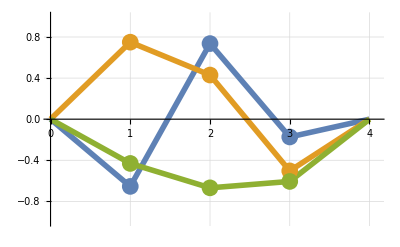

```mathematica
plt = Show[ListLinePlot[Table[Thread[{{0,1,2,3, 4},Insert[BiasedMassNM,0,{{1,1},{1,4},{2,1},{2,4},{3,1},{3,4}}][[k]]}],{k,3}],PlotStyle->{Thickness[0.01]},GridLines->Automatic,PlotRange->{{0,4.1},{-1,1}}],ListPlot[Table[Thread[{{1,2,3},BiasedMassNM[[k]]}],{k,3}],PlotStyle->PointSize[0.03],GridLines->Automatic]]
```

It is clear that the mode shapes of the system with a mass bias are very similar to the mode shapes of the system with equal masses, but there are also some distinct differences. The third mode corresponds to the lowest frequency in the system (indicated in green on the figure) is entirely the opposite phase between the two systems. The other two modes clearly look very similar to the shapes from the system with equal masses, but there is a strong bias toward the third (heavier) mass. The oscillations of the system here lose some of their symmetric behavior as well.